```mathematica
Clear[g,V]
```

```mathematica
Subscript[g, xy][x_,y_]:=(y-x)/L
Subscript[g, yx][x_,y_]:=1+(y-x)/L
```

```mathematica
V[x_]:=Piecewise[{{ΔV x / (a L),x<a L},{ΔV (L-x) / ((1-a) L),x≥a L}}]
```

```mathematica
Z[β_]:=L/(β ΔV) ( 1- Exp[-β ΔV ] )
```

```mathematica
inner[f_]:=Integrate[Subscript[g, yx][x,y] f[y],{y,0,x},Assumptions->x>0]+Integrate[Subscript[g, xy][x,y] f[y],{y,x,L},Assumptions->x<L]
```

```mathematica
full[f_,g_]:=Integrate[f[x] inner[g],{x,0,L},Assumptions->L>0]
```

```mathematica
fVV=Simplify[full[Exp[β V[#]]&,Exp[-β V[#]]&],Assumptions->L>0&&0<a<1&&ΔV>0&&β>0]
```

1/(β^3 ΔV^3)ⅇ^(-(a β ΔV)/(-1+a)) L^2 (-2 ⅇ^((2+1/(-1+a)) β ΔV)+5 a ⅇ^((2+1/(-1+a)) β ΔV)-3 a^2 ⅇ^((2+1/(-1+a)) β ΔV)-2 ⅇ^((β ΔV)/(-1+a))+5 a ⅇ^((β ΔV)/(-1+a))-3 a^2 ⅇ^((β ΔV)/(-1+a))+4 ⅇ^((a β ΔV)/(-1+a))-8 a ⅇ^((a β ΔV)/(-1+a))+ⅇ^((2+1/(-1+a)) β ΔV) β ΔV-2 a ⅇ^((2+1/(-1+a)) β ΔV) β ΔV+a^2 ⅇ^((2+1/(-1+a)) β ΔV) β ΔV+a ⅇ^((β ΔV)/(-1+a)) β ΔV-a^2 ⅇ^((β ΔV)/(-1+a)) β ΔV-ⅇ^((a β ΔV)/(-1+a)) β ΔV+ⅇ^((a β ΔV)/(-1+a)) β^2 ΔV^2-2 a ⅇ^((a β ΔV)/(-1+a)) β^2 ΔV^2+a ⅇ^((a β ΔV)/(-1+a)) (-2+6 a+β ΔV) Cosh[β ΔV]-a (-1+2 a) ⅇ^((a β ΔV)/(-1+a)) β ΔV Sinh[β ΔV])

```mathematica
fVc=Simplify[full[Exp[β V[#]]&,Exp[-β c V[#]]&],Assumptions->L>0&&0<a<1&&ΔV>0&&β>0&&0<c<1]
```

-1/((-1+c) c^2 β^3 ΔV^3)ⅇ^(-((1-2 c+a (-1+3 c)) β ΔV)/(-1+a)) L^2 ((-1+c) ⅇ^(((-2+3 a) c β ΔV)/(-1+a)) (1+c-c β ΔV+a (-2+c (-2+β ΔV)))-ⅇ^(((-1+2 a) c β ΔV)/(-1+a)) (-1+c^2 (1-β ΔV)+a (1+c) (2+c (-2+β ΔV)))+ⅇ^(((1-2 c+a (-1+3 c)) β ΔV)/(-1+a)) (1-c^2-c β ΔV+a (1+c) (-2+c (2+β ΔV)))-(-1+c) ⅇ^((-1+(2+1/(-1+a)) c) β ΔV) (-1-c+a (2+c (2+β ΔV))))

```mathematica
j1=-Simplify[(fVc/(Z[β c] Z[-β]) - fVV/(Z[β]Z[-β])),Assumptions->L>0&&0<a<1&&ΔV>0&&β>0&&0<c<1]
```

1/((-1+ⅇ^(β ΔV)) β ΔV)(1/(-1+ⅇ^(β ΔV))(-2+ⅇ^(2 β ΔV) (-2+β ΔV)+ⅇ^(β ΔV) (4-β ΔV+β^2 ΔV^2)+a (4+β ΔV+ⅇ^(2 β ΔV) (4-β ΔV)-2 ⅇ^(β ΔV) (4+β^2 ΔV^2)))+1/((-1+c) c (1-ⅇ^(-c β ΔV)))ⅇ^(-((1-2 c+a (-1+3 c)) β ΔV)/(-1+a)) ((-1+c) ⅇ^(((-2+3 a) c β ΔV)/(-1+a)) (1+c-c β ΔV+a (-2+c (-2+β ΔV)))-ⅇ^(((-1+2 a) c β ΔV)/(-1+a)) (-1+c^2 (1-β ΔV)+a (1+c) (2+c (-2+β ΔV)))+ⅇ^(((1-2 c+a (-1+3 c)) β ΔV)/(-1+a)) (1-c^2-c β ΔV+a (1+c) (-2+c (2+β ΔV)))-(-1+c) ⅇ^((-1+(2+1/(-1+a)) c) β ΔV) (-1-c+a (2+c (2+β ΔV)))))

```mathematica
fcV=Simplify[full[Exp[ β c V[#]]&,Exp[-β V[#]]&],Assumptions->L>0&&0<a<1&&ΔV>0&&β>0&&0<c<1]
```

-1/((-1+c) c^2 β^3 ΔV^3)ⅇ^(-((-2+2 a+c) β ΔV)/(-1+a)) L^2 ((-1+c) ⅇ^(((-2+a (2+c)) β ΔV)/(-1+a)) (1+c-c β ΔV+a (-2+c (-2+β ΔV)))-ⅇ^(((-2+2 a+c) β ΔV)/(-1+a)) (-1+c^2 (1-β ΔV)+a (1+c) (2+c (-2+β ΔV)))+ⅇ^(((-1+a+a c) β ΔV)/(-1+a)) (1-c^2-c β ΔV+a (1+c) (-2+c (2+β ΔV)))-(-1+c) ⅇ^((1+c/(-1+a)) β ΔV) (-1-c+a (2+c (2+β ΔV))))

```mathematica
fcc=Simplify[full[Exp[ β c V[#]]&,Exp[-β c V[#]]&],Assumptions->L>0&&0<a<1&&ΔV>0&&β>0&&0<c<1]
```

1/(c^3 β^3 ΔV^3)ⅇ^(-((-2+3 a) c β ΔV)/(-1+a)) L^2 (ⅇ^(((-3+4 a) c β ΔV)/(-1+a)) (-2+c β ΔV+a (4-c β ΔV))+ⅇ^((1+a/(-1+a)) c β ΔV) (-2+a (4+c β ΔV))+ⅇ^(((-2+3 a) c β ΔV)/(-1+a)) (4-c β ΔV+c^2 β^2 ΔV^2-2 a (4+c^2 β^2 ΔV^2)))

```mathematica
jc=-FullSimplify[(fcV/(Z[-β c] Z[β]) - fcc/(Z[c β]Z[-c β])),Assumptions->L>0&&0<a<1&&ΔV>0&&β>0&&0<c<1]
```

-((2 (-1+2 a) ⅇ^(1/2 (1+2 c) β ΔV) (-c^2 β ΔV Cosh[(β ΔV)/2] (-1+Cosh[c β ΔV])+Sinh[(β ΔV)/2] ((-1+c) (2+c (-2+c β^2 ΔV^2))+2 (-1+c)^2 Cosh[c β ΔV]+c^2 β ΔV Sinh[c β ΔV])))/((-1+c) c (-1+ⅇ^(β ΔV)) (-1+ⅇ^(c β ΔV))^2 β ΔV))

```mathematica
jtot=FullSimplify[j1+jc,Assumptions->L>0&&0<a<1&&ΔV>0&&β>0&&0<c<1]
```

1/(8 (-1+c))(-1+2 a) Csch[(c β ΔV)/2]^2 (Csch[(β ΔV)/2]^2 (-(-1+c) β ΔV (-1-c+c Cosh[β ΔV]+Cosh[c β ΔV])+(1+c) (-1+Cosh[c β ΔV]) Sinh[β ΔV])-2 (1+c) Sinh[c β ΔV])

```mathematica
Limit[j1,c->0]
```

-((-1+2 a) (-4-β ΔV+ⅇ^(2 β ΔV) (-4+β ΔV)+2 ⅇ^(β ΔV) (4+β^2 ΔV^2)))/(2 (-1+ⅇ^(β ΔV))^2 β ΔV)

```mathematica
Limit[jc,c->0]
```

0

```mathematica
Series[j1,{c,1,2}]
```

1/(2 (-1+ⅇ^(β ΔV))^3 β ΔV)ⅇ^(β ΔV) (-4+8 a+4 ⅇ^(β ΔV)-8 a ⅇ^(β ΔV)+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))-4 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))-2 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))+4 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))-4 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))-2 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))+4 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))+4 β ΔV-8 a β ΔV+4 ⅇ^(β ΔV) β ΔV-8 a ⅇ^(β ΔV) β ΔV-4 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β ΔV+8 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β ΔV-4 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β ΔV+8 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β ΔV-2 a β^2 ΔV^2-2 ⅇ^(β ΔV) β^2 ΔV^2+2 a ⅇ^(β ΔV) β^2 ΔV^2+2 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β^2 ΔV^2+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β^2 ΔV^2-2 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β^2 ΔV^2+β^3 ΔV^3-2 a β^3 ΔV^3+ⅇ^(β ΔV) β^3 ΔV^3-2 a ⅇ^(β ΔV) β^3 ΔV^3) (c-1)+1/((-1+ⅇ^(β ΔV)) β ΔV)((-ⅇ^((a β ΔV)/(-1+a)) (-1+2 a+a β ΔV)+ⅇ^(((-1+2 a) β ΔV)/(-1+a)) (-1+2 a+a β ΔV)-((-1+2 a) ⅇ^((a β ΔV)/(-1+a)) β ΔV (-2+4 a+a β ΔV))/(-1+a)+((-2+3 a) ⅇ^(((-2+3 a) β ΔV)/(-1+a)) β ΔV (2-4 a-β ΔV+a β ΔV))/(-1+a)-ⅇ^(((-1+2 a) β ΔV)/(-1+a)) (1-2 a-β ΔV+a β ΔV)+ⅇ^(((-2+3 a) β ΔV)/(-1+a)) (1-2 a-β ΔV+a β ΔV)-((-1+2 a)^2 ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β^2 ΔV^2 (-β ΔV+2 a β ΔV))/(2 (-1+a)^2)+((-2+3 a)^2 ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β^2 ΔV^2 (-β ΔV+2 a β ΔV))/(2 (-1+a)^2)-((-1+2 a) ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β ΔV (2-4 a-2 β ΔV+3 a β ΔV))/(-1+a)+((-2+3 a) ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β ΔV (-2+4 a-β ΔV+3 a β ΔV))/(-1+a)) (-(ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)) β ΔV)/((-1+ⅇ^(β ΔV))^2)+(-ⅇ^(((1-2 a) β ΔV)/(-1+a))+((2-3 a) ⅇ^(((1-2 a) β ΔV)/(-1+a)) β ΔV)/(-1+a))/(1-ⅇ^(-β ΔV)))+1/(1-ⅇ^(-β ΔV))ⅇ^(((1-2 a) β ΔV)/(-1+a)) (-((-1+2 a) ⅇ^((a β ΔV)/(-1+a)) β ΔV (-1+2 a+a β ΔV))/(-1+a)+((-2+3 a) ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β ΔV (-1+2 a+a β ΔV))/(-1+a)-1/2 ⅇ^((a β ΔV)/(-1+a)) (2 β ΔV+(β ΔV)/(-1+a))^2 (-2+4 a+a β ΔV)-((-1+2 a) ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β ΔV (1-2 a-β ΔV+a β ΔV))/(-1+a)-((-1+2 a)^3 ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β^3 ΔV^3 (-β ΔV+2 a β ΔV))/(6 (-1+a)^3)+((-2+3 a)^3 ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β^3 ΔV^3 (-β ΔV+2 a β ΔV))/(6 (-1+a)^3)-((-1+2 a)^2 ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β^2 ΔV^2 (2-4 a-2 β ΔV+3 a β ΔV))/(2 (-1+a)^2)+((-2+3 a)^2 ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β^2 ΔV^2 (-2+4 a-β ΔV+3 a β ΔV))/(2 (-1+a)^2)+1/(2 (-1+a)^2)(-2+3 a) ⅇ^(((-2+3 a) β ΔV)/(-1+a)) β ΔV (-2+6 a-4 a^2-2 β ΔV+10 a β ΔV-10 a^2 β ΔV+2 β^2 ΔV^2-5 a β^2 ΔV^2+3 a^2 β^2 ΔV^2))+(-ⅇ^((a β ΔV)/(-1+a)) (-2+4 a+a β ΔV)+ⅇ^(((-2+3 a) β ΔV)/(-1+a)) (2-4 a-β ΔV+a β ΔV)-((-1+2 a) ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β ΔV (-β ΔV+2 a β ΔV))/(-1+a)+((-2+3 a) ⅇ^(((-1+2 a) β ΔV)/(-1+a)) β ΔV (-β ΔV+2 a β ΔV))/(-1+a)-ⅇ^(((-1+2 a) β ΔV)/(-1+a)) (2-4 a-2 β ΔV+3 a β ΔV)+ⅇ^(((-1+2 a) β ΔV)/(-1+a)) (-2+4 a-β ΔV+3 a β ΔV)) ((ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)) (1+ⅇ^(β ΔV)) β^2 ΔV^2)/(2 (-1+ⅇ^(β ΔV))^3)-(ⅇ^(β ΔV) β ΔV (-ⅇ^(((1-2 a) β ΔV)/(-1+a))+((2-3 a) ⅇ^(((1-2 a) β ΔV)/(-1+a)) β ΔV)/(-1+a)))/((-1+ⅇ^(β ΔV))^2)+(ⅇ^(((1-2 a) β ΔV)/(-1+a))-((2-3 a) ⅇ^(((1-2 a) β ΔV)/(-1+a)) β ΔV)/(-1+a)+((2-3 a)^2 ⅇ^(((1-2 a) β ΔV)/(-1+a)) β^2 ΔV^2)/(2 (-1+a)^2))/(1-ⅇ^(-β ΔV)))) (c-1)^2+O[c-1]^3

```mathematica
Series[jc,{c,1,2}]
```

-1/((-1+ⅇ^(β ΔV))^3 β ΔV)2 ((-1+2 a) ⅇ^((3 β ΔV)/2) (β ΔV Cosh[(β ΔV)/2] (1-Cosh[β ΔV]-1/2 β^2 ΔV^2 Cosh[β ΔV]-2 β ΔV Sinh[β ΔV])+Sinh[(β ΔV)/2] (-2+2 β^2 ΔV^2+2 Cosh[β ΔV]+2 β^2 ΔV^2 Cosh[β ΔV]+β ΔV Sinh[β ΔV]+1/2 β^3 ΔV^3 Sinh[β ΔV]))) (c-1)-1/((-1+ⅇ^(β ΔV)) β ΔV)2 ((-1+2 a) ((-(2 ⅇ^((5 β ΔV)/2) β ΔV)/((-1+ⅇ^(β ΔV))^3)+(-ⅇ^((3 β ΔV)/2)+ⅇ^((3 β ΔV)/2) β ΔV)/((-1+ⅇ^(β ΔV))^2)) (β ΔV Cosh[(β ΔV)/2] (1-Cosh[β ΔV]-1/2 β^2 ΔV^2 Cosh[β ΔV]-2 β ΔV Sinh[β ΔV])+Sinh[(β ΔV)/2] (-2+2 β^2 ΔV^2+2 Cosh[β ΔV]+2 β^2 ΔV^2 Cosh[β ΔV]+β ΔV Sinh[β ΔV]+1/2 β^3 ΔV^3 Sinh[β ΔV]))+1/((-1+ⅇ^(β ΔV))^2)ⅇ^((3 β ΔV)/2) (β ΔV Cosh[(β ΔV)/2] (-β^2 ΔV^2 Cosh[β ΔV]-β ΔV Sinh[β ΔV]-1/6 β^3 ΔV^3 Sinh[β ΔV])+Sinh[(β ΔV)/2] (β^2 ΔV^2+β^2 ΔV^2 Cosh[β ΔV]+1/6 β^4 ΔV^4 Cosh[β ΔV]+2 β ΔV Sinh[β ΔV]+β^3 ΔV^3 Sinh[β ΔV])))) (c-1)^2+O[c-1]^3

```mathematica
j11=1/(2 (-1+ⅇ^(β ΔV))^3 β ΔV)ⅇ^(β ΔV) (-4+8 a+4 ⅇ^(β ΔV)-8 a ⅇ^(β ΔV)+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))-4 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))-2 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))+4 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))-4 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))-2 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))+4 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))+4 β ΔV-8 a β ΔV+4 ⅇ^(β ΔV) β ΔV-8 a ⅇ^(β ΔV) β ΔV-4 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β ΔV+8 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β ΔV-4 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β ΔV+8 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β ΔV-2 a β^2 ΔV^2-2 ⅇ^(β ΔV) β^2 ΔV^2+2 a ⅇ^(β ΔV) β^2 ΔV^2+2 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β^2 ΔV^2+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β^2 ΔV^2-2 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β^2 ΔV^2+β^3 ΔV^3-2 a β^3 ΔV^3+ⅇ^(β ΔV) β^3 ΔV^3-2 a ⅇ^(β ΔV) β^3 ΔV^3) (c-1)
```

1/(2 (-1+ⅇ^(β ΔV))^3 β ΔV)(-1+c) ⅇ^(β ΔV) (-4+8 a+4 ⅇ^(β ΔV)-8 a ⅇ^(β ΔV)+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))-4 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))-2 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))+4 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a))+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))-4 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))-2 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))+4 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a))+4 β ΔV-8 a β ΔV+4 ⅇ^(β ΔV) β ΔV-8 a ⅇ^(β ΔV) β ΔV-4 ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β ΔV+8 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β ΔV-4 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β ΔV+8 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β ΔV-2 a β^2 ΔV^2-2 ⅇ^(β ΔV) β^2 ΔV^2+2 a ⅇ^(β ΔV) β^2 ΔV^2+2 a ⅇ^(β ΔV+((1-2 a) β ΔV)/(-1+a)+(a β ΔV)/(-1+a)) β^2 ΔV^2+2 ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β^2 ΔV^2-2 a ⅇ^(((1-2 a) β ΔV)/(-1+a)+((-2+3 a) β ΔV)/(-1+a)) β^2 ΔV^2+β^3 ΔV^3-2 a β^3 ΔV^3+ⅇ^(β ΔV) β^3 ΔV^3-2 a ⅇ^(β ΔV) β^3 ΔV^3)

```mathematica
jc1=-1/((-1+ⅇ^(β ΔV))^3 β ΔV)2 ((-1+2 a) ⅇ^((3 β ΔV)/2) (β ΔV Cosh[(β ΔV)/2] (1-Cosh[β ΔV]-1/2 β^2 ΔV^2 Cosh[β ΔV]-2 β ΔV Sinh[β ΔV])+Sinh[(β ΔV)/2] (-2+2 β^2 ΔV^2+2 Cosh[β ΔV]+2 β^2 ΔV^2 Cosh[β ΔV]+β ΔV Sinh[β ΔV]+1/2 β^3 ΔV^3 Sinh[β ΔV]))) (c-1)
```

-1/((-1+ⅇ^(β ΔV))^3 β ΔV)2 (-1+2 a) (-1+c) ⅇ^((3 β ΔV)/2) (β ΔV Cosh[(β ΔV)/2] (1-Cosh[β ΔV]-1/2 β^2 ΔV^2 Cosh[β ΔV]-2 β ΔV Sinh[β ΔV])+Sinh[(β ΔV)/2] (-2+2 β^2 ΔV^2+2 Cosh[β ΔV]+2 β^2 ΔV^2 Cosh[β ΔV]+β ΔV Sinh[β ΔV]+1/2 β^3 ΔV^3 Sinh[β ΔV]))

```mathematica
Simplify[j11+jc1,Assumptions->L>0&&0<a<1&&ΔV>0&&β>0&&0<c<1]
```

0

```mathematica
Series[Log[jtot],{c,0,3}]
```

Log[-1/(4 β ΔV)(-1+2 a) (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])]-(2 (6+β^2 ΔV^2-3 Csch[(β ΔV)/2]^2+3 Cosh[β ΔV] Csch[(β ΔV)/2]^2-3 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]) c)/(3 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]))+1/2 (-((4 (6+β^2 ΔV^2-3 Csch[(β ΔV)/2]^2+3 Cosh[β ΔV] Csch[(β ΔV)/2]^2-3 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])^2)/(9 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])^2))+(-24-6 β^2 ΔV^2+12 Csch[(β ΔV)/2]^2-β^2 ΔV^2 Csch[(β ΔV)/2]^2-12 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β^2 ΔV^2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+12 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])/(3 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]))) c^2+1/3 ((2 (6+β^2 ΔV^2-3 Csch[(β ΔV)/2]^2+3 Cosh[β ΔV] Csch[(β ΔV)/2]^2-3 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]) (-24-6 β^2 ΔV^2+12 Csch[(β ΔV)/2]^2-β^2 ΔV^2 Csch[(β ΔV)/2]^2-12 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β^2 ΔV^2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+12 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]))/(9 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])^2)+(-360-90 β^2 ΔV^2+2 β^4 ΔV^4+180 Csch[(β ΔV)/2]^2-15 β^2 ΔV^2 Csch[(β ΔV)/2]^2-180 Cosh[β ΔV] Csch[(β ΔV)/2]^2+15 β^2 ΔV^2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+180 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])/(30 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]))-(2 (6+β^2 ΔV^2-3 Csch[(β ΔV)/2]^2+3 Cosh[β ΔV] Csch[(β ΔV)/2]^2-3 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]) ((4 (6+β^2 ΔV^2-3 Csch[(β ΔV)/2]^2+3 Cosh[β ΔV] Csch[(β ΔV)/2]^2-3 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])^2)/(9 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])^2)-(-24-6 β^2 ΔV^2+12 Csch[(β ΔV)/2]^2-β^2 ΔV^2 Csch[(β ΔV)/2]^2-12 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β^2 ΔV^2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+12 β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV])/(6 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]))))/(3 (-4+2 Csch[(β ΔV)/2]^2+β^2 ΔV^2 Csch[(β ΔV)/2]^2-2 Cosh[β ΔV] Csch[(β ΔV)/2]^2+β ΔV Csch[(β ΔV)/2]^2 Sinh[β ΔV]))) c^3+O[c]^4

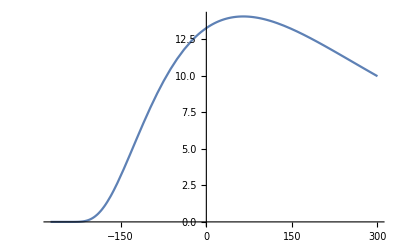

```mathematica
Plot[lu lb / (lu + lb )L jtot//.{a->1/4,ΔV->40,β->310.15/(4.28( T+273.15)),L->8,lu->40,lb->80,c->0.2},{T,-273.15,300},PlotRange->All]
```

```mathematica
Limit[lu lb / (lu + lb )L jtot//.{a->1/4,ΔV->40,β->1/4.28,L->8,lu->40,lb->80},c->0.3]
```

7.85977

```mathematica
Series[j1,{β,0,3}]
```

1/720 (2 ΔV^3-4 a ΔV^3-c ΔV^3+2 a c ΔV^3-c^2 ΔV^3+2 a c^2 ΔV^3) β^3+O[β]^4

```mathematica
Series[jc,{β,0,3}]
```

-1/720 ((-1+c) (-c ΔV^3+2 a c ΔV^3-2 c^2 ΔV^3+4 a c^2 ΔV^3)) β^3+O[β]^4

```mathematica
fVVV=Simplify[full[Exp[β V[#]]&,V[#] Exp[-β V[#]]&],Assumptions->L>0&&0<a<1&&ΔV>0&&β>0]
```

-1/(2 β^4 ΔV^3)ⅇ^(-β ΔV) L^2 (6+4 β ΔV+ⅇ^(2 β ΔV) (6-2 β ΔV)-ⅇ^(β ΔV) (12+2 β ΔV+β^3 ΔV^3)+2 a (-6-5 β ΔV-β^2 ΔV^2+ⅇ^(2 β ΔV) (-6+β ΔV)+ⅇ^(β ΔV) (12+4 β ΔV+β^2 ΔV^2+β^3 ΔV^3)))

```mathematica
FullSimplify[β(fVVV+Simplify[D[Log[Z[β]],β]] fVV)/(Z[β] Z[-β]),Assumptions->L>0&&0<a<1&&ΔV>0&&β>0]
```

-1/(2 (-1+ⅇ^(β ΔV))^3 β ΔV)(-1+2 a) ⅇ^(-(a β ΔV)/(-1+a)) (2 ⅇ^((a β ΔV)/(-1+a))-2 ⅇ^(((-3+4 a) β ΔV)/(-1+a))+ⅇ^((2+1/(-1+a)) β ΔV) (-6+β^3 ΔV^3)+ⅇ^((3+1/(-1+a)) β ΔV) (6+β^3 ΔV^3))

```mathematica
FullSimplify[%/(a-1/2)(1-Exp[-β ΔV])^3,Assumptions->L>0&&0<a<1&&ΔV>0&&β>0]
```

(ⅇ^(-(4+1/(-1+a)) β ΔV) (2 ⅇ^((4+1/(-1+a)) β ΔV)-2 ⅇ^((a β ΔV)/(-1+a))+ⅇ^((2+1/(-1+a)) β ΔV) (6-β^3 ΔV^3)-ⅇ^((3+1/(-1+a)) β ΔV) (6+β^3 ΔV^3)))/(β ΔV)

```mathematica
Expand[%]
```

2/(β ΔV)+(6 ⅇ^((2+1/(-1+a)) β ΔV-(4+1/(-1+a)) β ΔV))/(β ΔV)-(6 ⅇ^((3+1/(-1+a)) β ΔV-(4+1/(-1+a)) β ΔV))/(β ΔV)-(2 ⅇ^(-(4+1/(-1+a)) β ΔV+(a β ΔV)/(-1+a)))/(β ΔV)-ⅇ^((2+1/(-1+a)) β ΔV-(4+1/(-1+a)) β ΔV) β^2 ΔV^2-ⅇ^((3+1/(-1+a)) β ΔV-(4+1/(-1+a)) β ΔV) β^2 ΔV^2

```mathematica
Map[Simplify[#]&,%]
```

2/(β ΔV)-(2 ⅇ^(-3 β ΔV))/(β ΔV)+(6 ⅇ^(-2 β ΔV))/(β ΔV)-(6 ⅇ^(-β ΔV))/(β ΔV)-ⅇ^(-2 β ΔV) β^2 ΔV^2-ⅇ^(-β ΔV) β^2 ΔV^2

```mathematica
FullSimplify[β(fVVV+Simplify[D[Log[Z[β]],β]] fVV)/(Z[β] Z[-β])-(a-1/2)(2/(β ΔV)-(β ΔV)^2 Exp[-β ΔV](1+Exp[-β ΔV])(1-Exp[-β ΔV])^-3),Assumptions->L>0&&0<a<1&&ΔV>0&&β>0]
```

0

```mathematica
Series[(a-1/2)(2/(β ΔV)-(β ΔV)^2/4Cosh[β ΔV / 2](Sinh[β ΔV/2])^-3),{β,0,4}]
```

(-ΔV^3/240+(a ΔV^3)/120) β^3+O[β]^5

```mathematica
NSolve[(D[jtot,β]==0)/.{ΔV->40,a->1/4,c->3/10},β]
```

ReplaceAll::reps: {{ΔV → 40, a → 1/4, c → 3/10} == 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(ΔV → 40) == 0 && (a → 1/4) == 0 && (c → 3/10) == 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-1/(8 (-1+c))(-1+2 a) c ΔV Coth[(c β ΔV)/2] Csch[(c β ΔV)/2]^2 (Csch[(β ΔV)/2]^2 (-(-1+c) β ΔV (-1-c+c Cosh[β ΔV]+Cosh[c β ΔV])+(1+c) (-1+Cosh[c β ΔV]) Sinh[β ΔV])-2 (1+c) Sinh[c β ΔV])+1/(8 (-1+c))(-1+2 a) Csch[(c β ΔV)/2]^2 (-2 c (1+c) ΔV Cosh[c β ΔV]-ΔV Coth[(β ΔV)/2] Csch[(β ΔV)/2]^2 (-(-1+c) β ΔV (-1-c+c Cosh[β ΔV]+Cosh[c β ΔV])+(1+c) (-1+Cosh[c β ΔV]) Sinh[β ΔV])+Csch[(β ΔV)/2]^2 ((1+c) ΔV Cosh[β ΔV] (-1+Cosh[c β ΔV])-(-1+c) ΔV (-1-c+c Cosh[β ΔV]+Cosh[c β ΔV])+c (1+c) ΔV Sinh[β ΔV] Sinh[c β ΔV]-(-1+c) β ΔV (c ΔV Sinh[β ΔV]+c ΔV Sinh[c β ΔV])))/.{ΔV→40,a→1/4,c→3/10}==0,β]